## Exercises

For the exam complete two of these... 

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

Q1

```mathematica
f[x_]:= x(Exp[-x])+x(1-x)
```

```mathematica
f[0]
f[0.1]
f[0.2]
f[0.4]
f[0.8]
```

0

0.180484

0.323746

0.508128

0.519463

Q2

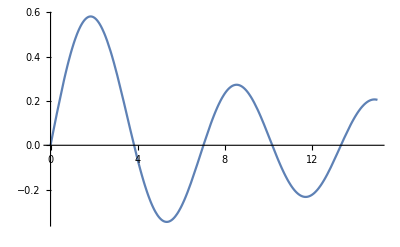

```mathematica
Plot[BesselJ[1,x],{x,0,15}]
```

```mathematica
FindRoot[BesselJ[1,x]==0,{x,4}]
FindRoot[BesselJ[1,x]==0,{x,7}]
FindRoot[BesselJ[1,x]==0,{x,10}]
```

{x→3.83171}

{x→7.01559}

{x→10.1735}

Q3

```mathematica
f[x_]:=Sin[x]Exp[-x]
```

```mathematica
D[f[x],x]
```

ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

```mathematica
F=Integrate[f[x],x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
Simplify[D[F,x]]
```

ⅇ^-x Sin[x]

Q4

```mathematica
fzero=Series[Exp[ArcTan[x]],{x,0,10}]
```

1+x+x^2/2-x^3/6-(7 x^4)/24+x^5/24+(29 x^6)/144-x^7/1008-(1219 x^8)/8064-(1163 x^9)/72576+(17321 x^10)/145152+O[x]^11

```mathematica
finf=Series[Exp[ArcTan[x]],{x,∞,10}]
```

ⅇ^(π/2)-ⅇ^(π/2)/x+ⅇ^(π/2)/(2 x^2)+ⅇ^(π/2)/(6 x^3)-(7 ⅇ^(π/2))/(24 x^4)-ⅇ^(π/2)/(24 x^5)+(29 ⅇ^(π/2))/(144 x^6)+ⅇ^(π/2)/(1008 x^7)-(1219 ⅇ^(π/2))/(8064 x^8)+(1163 ⅇ^(π/2))/(72576 x^9)+(17321 ⅇ^(π/2))/(145152 x^10)+O[1/x]^11

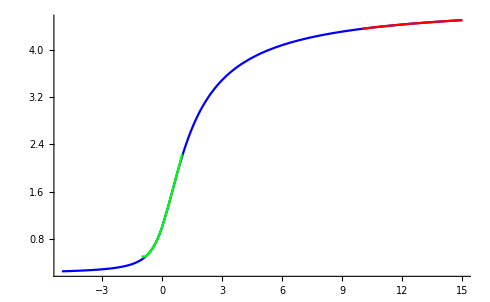

```mathematica
Show[
Plot[Exp[ArcTan[x]],{x,-5,15},PlotStyle->Blue],
Plot[Evaluate[Normal[fzero]],{x,-1,1},PlotStyle->Green],Plot[Evaluate[Normal[finf]],{x,10,15},PlotStyle->Red],
PlotRange->All,AxesOrigin->{0,0}]
```

Q6

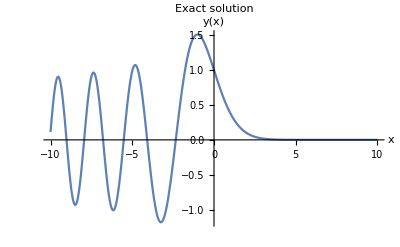

```mathematica
exactsol =DSolve[{y''[x]-x* y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y[x],x];
sol=y[x]/.exactsol[[1]];
Plot[sol,{x,-10,10},PlotLabel->"Exact solution",AxesLabel->{"x","y(x)"}]
```

{{y→InterpolatingFunction[…]}}

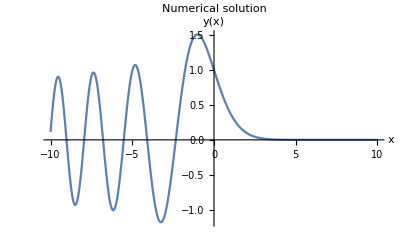

```mathematica
approxsol=NDSolve[{y''[x]-x* y[x]==0,
                                       y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},
                                          y,{x,-10,10},
				     Method->"ImplicitRungeKutta",AccuracyGoal->13,     PrecisionGoal->13,MaxSteps->Infinity]
ynum=(y/.Flatten@approxsol)[x];
Plot[ynum,{x,-10,10},PlotLabel->"Numerical solution",AxesLabel->{"x","y(x)"}]
```